```mathematica
Quit;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/Dhybrid/math

```mathematica
<<init`
```

```mathematica
Mpl=2435/1000 10^18;(*GeV*)
M=10^16/Mpl;
ϕc=1;
Π2=61;
μ1=Π2/(M^2 ϕc);μ1//N
μ2=10;
Λ=(27 10^12)/Mpl Sqrt[μ1/(4 10^6)];Λ//N
dNPT=Π2/8;dNPT//N
ϕi=ϕc+dNPT/μ1;
ϕi-ϕc//N
```

3.61683×10^6

0.0000105438

7.625

2.1082×10^-6

### D > 10

```mathematica
ψs={ψ1[NN],ψ2[NN],ψ3[NN],ψ4[NN],ψ5[NN],ψ6[NN],ψ7[NN],ψ8[NN],ψ9[NN],ψ10[NN],
ψ11[NN],ψ12[NN],ψ13[NN],ψ14[NN],ψ15[NN],ψ16[NN],ψ17[NN],ψ18[NN],ψ19[NN],ψ20[NN],
ψ21[NN],ψ22[NN],ψ23[NN],ψ24[NN],ψ25[NN],ψ26[NN],ψ27[NN],ψ28[NN],ψ29[NN],ψ30[NN],
ψ31[NN],ψ32[NN],ψ33[NN],ψ34[NN],ψ35[NN],ψ36[NN],ψ37[NN],ψ38[NN],ψ39[NN],ψ40[NN],
ψ41[NN],ψ42[NN],ψ43[NN],ψ44[NN],ψ45[NN],ψ46[NN],ψ47[NN],ψ48[NN],ψ49[NN],ψ50[NN],
ψ51[NN],ψ52[NN],ψ53[NN],ψ54[NN],ψ55[NN],ψ56[NN],ψ57[NN],ψ58[NN],ψ59[NN],ψ60[NN],
ψ61[NN],ψ62[NN],ψ63[NN],ψ64[NN],ψ65[NN],ψ66[NN],ψ67[NN],ψ68[NN],ψ69[NN],ψ70[NN],
ψ71[NN],ψ72[NN],ψ73[NN],ψ74[NN],ψ75[NN],ψ76[NN],ψ77[NN],ψ78[NN],ψ79[NN],ψ80[NN],
ψ81[NN],ψ82[NN],ψ83[NN],ψ84[NN],ψ85[NN],ψ86[NN],ψ87[NN],ψ88[NN],ψ89[NN],ψ90[NN],
ψ91[NN],ψ92[NN],ψ93[NN],ψ94[NN],ψ95[NN],ψ96[NN],ψ97[NN],ψ98[NN],ψ99[NN],ψ100[NN]};
ws={w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,
w11,w12,w13,w14,w15,w16,w17,w18,w19,w20,
w21,w22,w23,w24,w25,w26,w27,w28,w29,w30,
w31,w32,w33,w34,w35,w36,w37,w38,w39,w40,
w41,w42,w43,w44,w45,w46,w47,w48,w49,w50,
w51,w52,w53,w54,w55,w56,w57,w58,w59,w60,
w61,w62,w63,w64,w65,w66,w67,w68,w69,w70,
w71,w72,w73,w74,w75,w76,w77,w78,w79,w80,
w81,w82,w83,w84,w85,w86,w87,w88,w89,w90,
w91,w92,w93,w94,w95,w96,w97,w98,w99,w100,
wϕ};
fields={ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,ψ7,ψ8,ψ9,ψ10,
ψ11,ψ12,ψ13,ψ14,ψ15,ψ16,ψ17,ψ18,ψ19,ψ20,
ψ21,ψ22,ψ23,ψ24,ψ25,ψ26,ψ27,ψ28,ψ29,ψ30,
ψ31,ψ32,ψ33,ψ34,ψ35,ψ36,ψ37,ψ38,ψ39,ψ40,
ψ41,ψ42,ψ43,ψ44,ψ45,ψ46,ψ47,ψ48,ψ49,ψ50,
ψ51,ψ52,ψ53,ψ54,ψ55,ψ56,ψ57,ψ58,ψ59,ψ60,
ψ61,ψ62,ψ63,ψ64,ψ65,ψ66,ψ67,ψ68,ψ69,ψ70,
ψ71,ψ72,ψ73,ψ74,ψ75,ψ76,ψ77,ψ78,ψ79,ψ80,
ψ81,ψ82,ψ83,ψ84,ψ85,ψ86,ψ87,ψ88,ψ89,ψ90,
ψ91,ψ92,ψ93,ψ94,ψ95,ψ96,ψ97,ψ98,ψ99,ψ100,
ϕ};
n=Length[ψs]
$Assumptions=Table[ψs[[i]]>0,{i,n}];
```

100

```mathematica
V=Λ^4(1+2(ϕ[NN]^2-ϕc^2)/ϕc^2 Norm[ψs]^2/M^2+(ϕ[NN]-ϕc)/μ1-(ϕ[NN]-ϕc)^2/μ2^2)//Simplify;
```

```mathematica
Vϕ=D[V, ϕ[NN]];
Vψs=Table[D[V, ψs[[i]]],{i,n}];
```

```mathematica
(*EoM=Join[Table[ⅆψs[[i]]==(-Vψs[[i]])/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[i]][NN],{i,n}],{ⅆϕ[NN]==-Vϕ/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[n+1]][NN]}];*)
EoM=Join[Table[ⅆψs[[i]]==(-Vψs[[i]])/Λ^4 ⅆNN+1/(2π)Sqrt[Λ^4/3]ⅆws[[i]][NN],{i,n}],{ⅆϕ[NN]==-Vϕ/Λ^4 ⅆNN+1/(2π)Sqrt[Λ^4/3]ⅆws[[n+1]][NN]}];
```

```mathematica
proc=ItoProcess[EoM,Join[ψs,{ϕ[NN]}],{fields,Join[Table[0,{i,n}],{ϕi}]},NN,Table[ws[[i]]\[Distributed]WienerProcess[],{i,n}]];//AbsoluteTiming
```

{0.919523,Null}

```mathematica
AbsoluteTiming[sol=RandomFunction[proc,{0,2dNPT,0.01},10];
ϕsol=Table[{sol["Path",1][[i,1]]-dNPT,Abs[(sol["Path",1][[i,2,n+1]]-ϕc)/ϕc]},{i,Length[sol["Path"]]}];
ψssol=Table[{sol["Path",1][[i,1]]-dNPT,(sol["Path",1][[i,2,j]])/M},{j,n},{i,Length[sol["Path"]]}];
ψrsol=Table[{sol["Path",p][[i,1]]-dNPT,Sqrt[Sum[(sol["Path",p][[i,2,j]])^2,{j,n}]]/M},{p,10},{i,Length[sol["Path"]]}];
θsol=Table[{sol["Path",p][[i,1]]-dNPT,ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]]},{p,10},{i,2,Length[sol["Path"]]}];
polarsol=Table[{ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]],sol["Path",p][[i,1]]},{p,10},{i,2,Length[sol["Path"]]}];]
```

{137.98,Null}

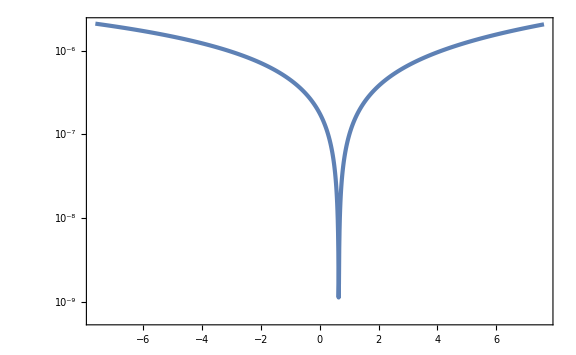

```mathematica
ListLogPlot[ϕsol]
```

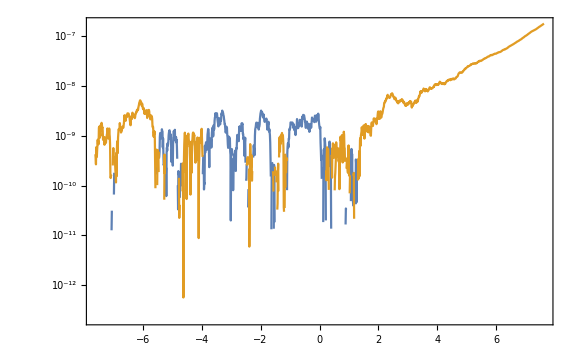

```mathematica
ListLogPlot[{ψssol[[1]],ψssol[[1]].DiagonalMatrix[{1,-1}]},PlotStyle->Automatic]
```

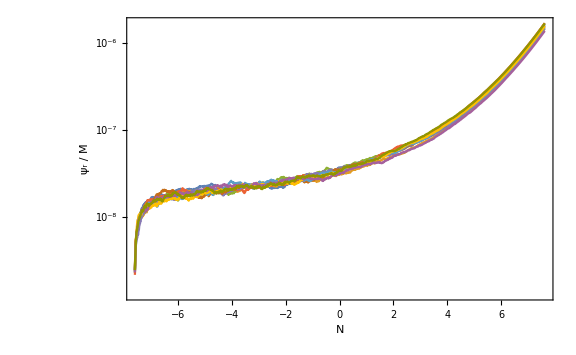

```mathematica
ListLogPlot[ψrsol,PlotStyle->Automatic,FrameLabel->{N,Row[{Subscript[ψ, r]," / M"}]}]
```

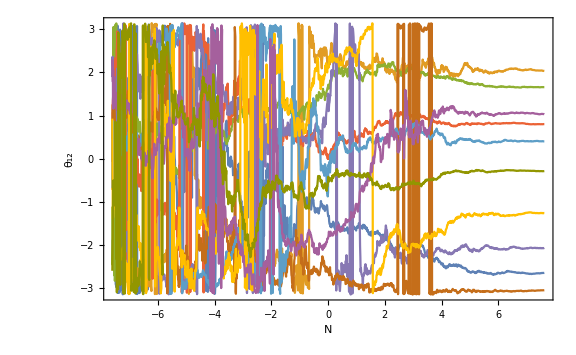

```mathematica
ListPlot[θsol,PlotStyle->Automatic,FrameLabel->{N,Subscript[θ, 12]}]
```

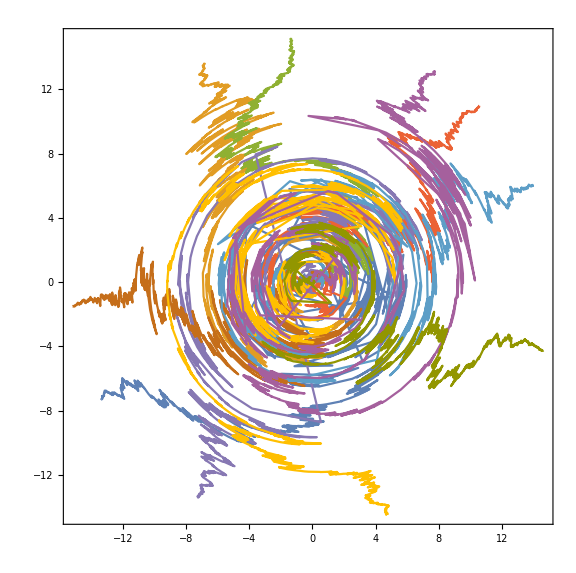

```mathematica
ListPolarPlot[polarsol,PlotStyle->Automatic]
```

### D = 10

```mathematica
ψs={ψ1[NN],ψ2[NN],ψ3[NN],ψ4[NN],ψ5[NN],ψ6[NN],ψ7[NN],ψ8[NN],ψ9[NN],ψ10[NN]};
ws={w1,w2,w3,w4,w5,w6,w7,w8,w9,w10,wϕ};
fields={ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,ψ7,ψ8,ψ9,ψ10,ϕ};
n=Length[ψs];
$Assumptions=Table[ψs[[i]]>0,{i,n}];
```

```mathematica
V=Λ^4(1+2(ϕ[NN]^2-ϕc^2)/ϕc^2 Norm[ψs]^2/M^2+(ϕ[NN]-ϕc)/μ1-(ϕ[NN]-ϕc)^2/μ2^2)//Simplify;
```

```mathematica
Vϕ=D[V, ϕ[NN]];
Vψs=Table[D[V, ψs[[i]]],{i,n}];
```

```mathematica
EoM=Join[Table[ⅆψs[[i]]==(-Vψs[[i]])/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[i]][NN],{i,n}],{ⅆϕ[NN]==-Vϕ/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[n+1]][NN]}];
```

```mathematica
proc=ItoProcess[EoM,Join[ψs,{ϕ[NN]}],{fields,Join[Table[0,{i,n}],{ϕi}]},NN,Table[ws[[i]]\[Distributed]WienerProcess[],{i,n}]];
```

```mathematica
AbsoluteTiming[sol=RandomFunction[proc,{0,2dNPT,0.01},10];
ϕsol=Table[{sol["Path",1][[i,1]]-dNPT,Abs[(sol["Path",1][[i,2,n+1]]-ϕc)/ϕc]},{i,Length[sol["Path"]]}];
ψssol=Table[{sol["Path",1][[i,1]]-dNPT,(sol["Path",1][[i,2,j]])/M},{j,n},{i,Length[sol["Path"]]}];
ψrsol=Table[{sol["Path",p][[i,1]]-dNPT,Sqrt[Sum[(sol["Path",p][[i,2,j]])^2,{j,n}]]/M},{p,10},{i,Length[sol["Path"]]}];
θsol=Table[{sol["Path",p][[i,1]]-dNPT,ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]]},{p,10},{i,2,Length[sol["Path"]]}];
polarsol=Table[{ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]],sol["Path",p][[i,1]]},{p,10},{i,2,Length[sol["Path"]]}];]
```

{20.7186,Null}

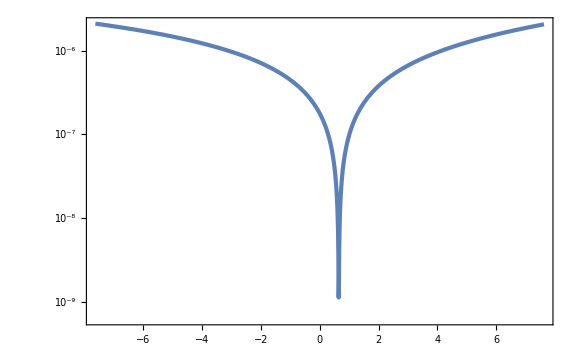

```mathematica
ListLogPlot[ϕsol]
```

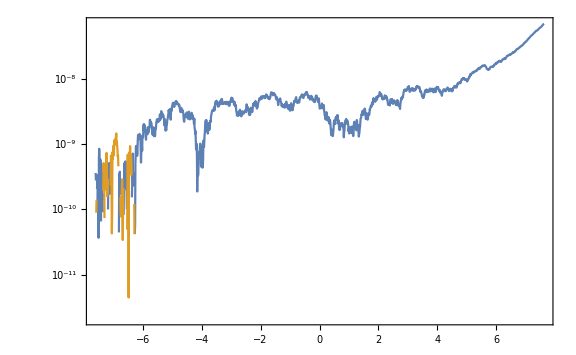

```mathematica
ListLogPlot[{ψssol[[1]],ψssol[[1]].DiagonalMatrix[{1,-1}]},PlotStyle->Automatic]
```

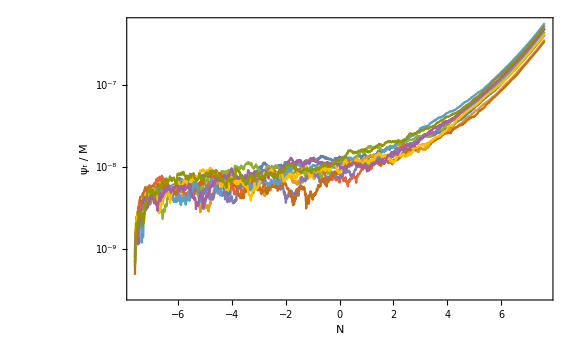

```mathematica
ListLogPlot[ψrsol,PlotStyle->Automatic,FrameLabel->{N,Row[{Subscript[ψ, r]," / M"}]}]
```

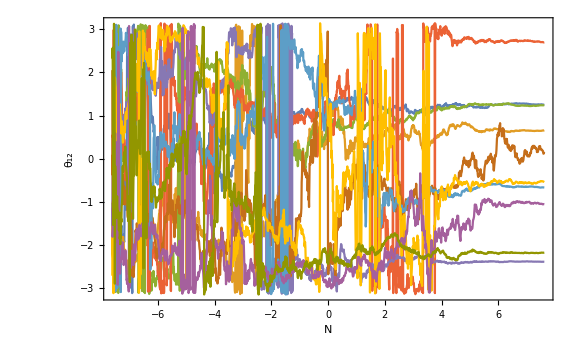

```mathematica
ListPlot[θsol,PlotStyle->Automatic,FrameLabel->{N,Subscript[θ, 12]}]
```

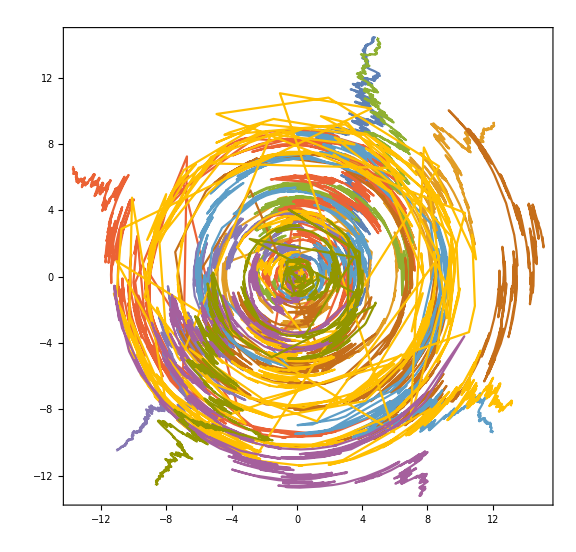

```mathematica
ListPolarPlot[polarsol,PlotStyle->Automatic]
```

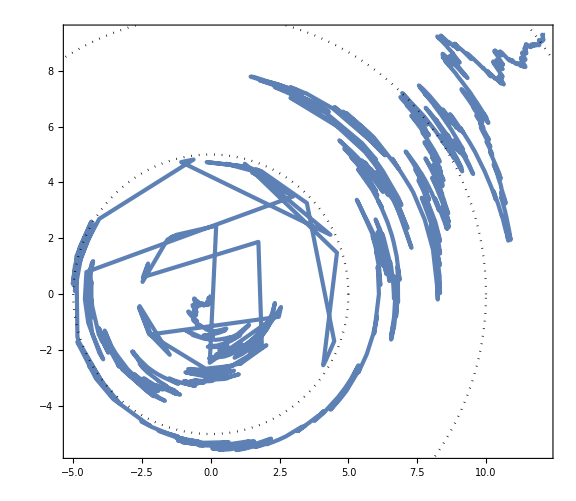

```mathematica
Show[ListPolarPlot[polarsol[[2]]],PolarPlot[{5,10,15},{θ,0,2π},PlotStyle->{{Black,Dotted}}]]
```

### D = 2

```mathematica
ψs={ψ1[NN],ψ2[NN]};
ws={w1,w2,wϕ};
fields={ψ1,ψ2,ϕ};
n=Length[ψs];
$Assumptions=Table[ψs[[i]]>0,{i,n}];
```

```mathematica
V=Λ^4(1+2(ϕ[NN]^2-ϕc^2)/ϕc^2 Norm[ψs]^2/M^2+(ϕ[NN]-ϕc)/μ1-(ϕ[NN]-ϕc)^2/μ2^2)//Simplify;
```

```mathematica
Vϕ=D[V, ϕ[NN]];
Vψs=Table[D[V, ψs[[i]]],{i,n}];
```

```mathematica
EoM=Join[Table[ⅆψs[[i]]==(-Vψs[[i]])/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[i]][NN],{i,n}],{ⅆϕ[NN]==-Vϕ/V ⅆNN+1/(2π)Sqrt[V/3]ⅆws[[n+1]][NN]}];
```

```mathematica
proc=ItoProcess[EoM,Join[ψs,{ϕ[NN]}],{fields,Join[Table[0,{i,n}],{ϕi}]},NN,Table[ws[[i]]\[Distributed]WienerProcess[],{i,n}]];
```

```mathematica
AbsoluteTiming[sol=RandomFunction[proc,{0,2dNPT,0.01},10];
ϕsol=Table[{sol["Path",1][[i,1]]-dNPT,Abs[(sol["Path",1][[i,2,n+1]]-ϕc)/ϕc]},{i,Length[sol["Path"]]}];
ψssol=Table[{sol["Path",1][[i,1]]-dNPT,(sol["Path",1][[i,2,j]])/M},{j,n},{i,Length[sol["Path"]]}];
ψrsol=Table[{sol["Path",p][[i,1]]-dNPT,Sqrt[Sum[(sol["Path",p][[i,2,j]])^2,{j,n}]]/M},{p,10},{i,Length[sol["Path"]]}];
θsol=Table[{sol["Path",p][[i,1]]-dNPT,ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]]},{p,10},{i,2,Length[sol["Path"]]}];
polarsol=Table[{ArcTan[sol["Path",p][[i,2,1]],sol["Path",p][[i,2,2]]],sol["Path",p][[i,1]]},{p,10},{i,2,Length[sol["Path"]]}];]
```

{9.35752,Null}

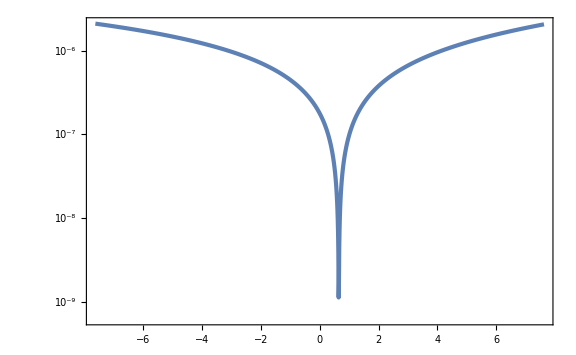

```mathematica
ListLogPlot[ϕsol]
```

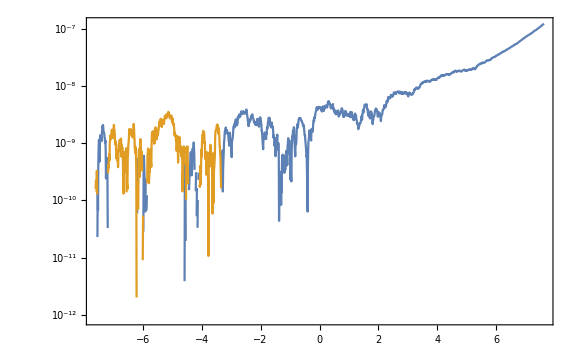

```mathematica
ListLogPlot[{ψssol[[1]],ψssol[[1]].DiagonalMatrix[{1,-1}]},PlotStyle->Automatic]
```

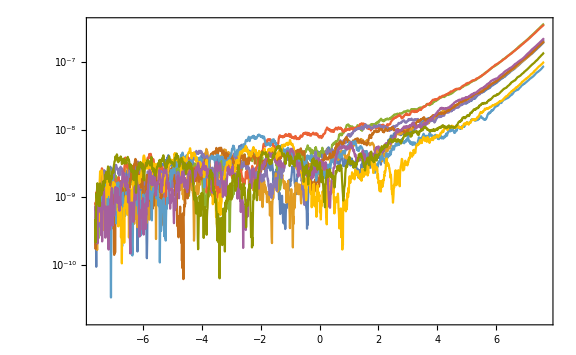

```mathematica
ListLogPlot[ψrsol,PlotStyle->Automatic]
```

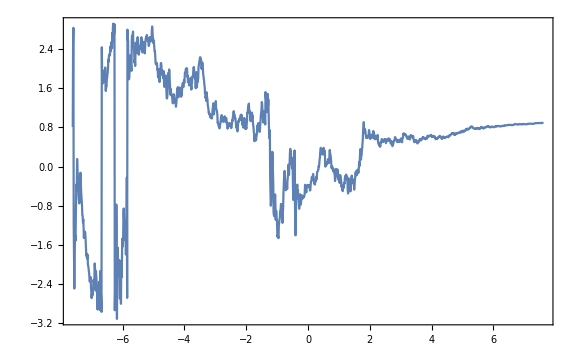

```mathematica
ListPlot[θsol[[1]],PlotStyle->Automatic]
```

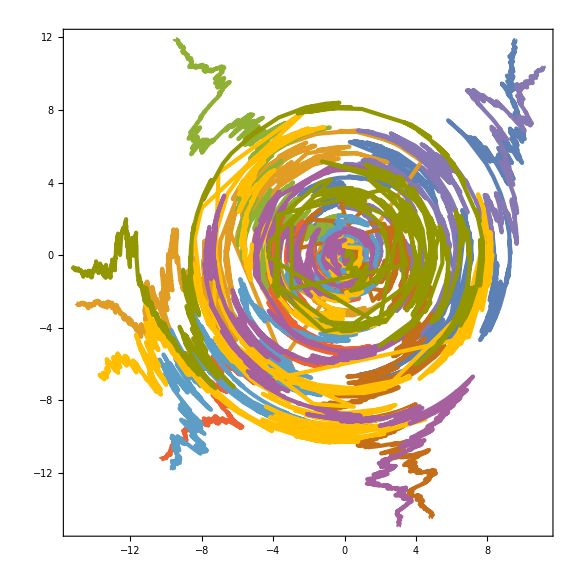

```mathematica
ListPolarPlot[polarsol]
```